```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
Subscript[Ω, m0]=0.315;  H02=(67.37)^2; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]=  3 10^(-4);
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Friedmann= (1+z)(β/2) y'[z] - α y[z]  + (  y[z] -Subscript[Ω, m0] H02(1+z)^3 -Subscript[Ω, r0] H02(1+z)^4  )^(2/(2-Δ)) ==0
```

-α y[z]+(-1429.7 (1+z)^3-1.36162 (1+z)^4+y[z])^(2/(2-Δ))+1/2 (1+z) β y'[z]==0

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Hubbledata=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat"] //TableForm ;
```

```mathematica
zexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,1}][[2;;-1]];
```

```mathematica
Hexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,2}][[2;;-1]];
```

```mathematica
Sigexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,3}][[2;;-1]];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
H[zH_,alpha_,beta_,Delta_]:=Sqrt[NDSolveValue[{Friedmann, y[0]==H02}/. {α-> alpha,β-> beta,Δ-> Delta } ,y[z],{z,zH},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10][[0]][zH]];
```

```mathematica
Chi[HEXP_,HTEO_,SigEXP_]:= N[(HEXP-HTEO)^(2) / (SigEXP)^2 ];
```

```mathematica
Chi2[α_,β_,Δ_]:=  Sum[Chi[Hexp[[i]],N[Re[H[zexp[[i]],α,β,Δ]]],Sigexp[[i]]],{i,1,36}];
```

```mathematica
Dimensions[Range[0.3,0.9,0.01]]
```

{61}

```mathematica
Dimensions[Range[0.7,1.,0.005]]
```

{61}

```mathematica
Dimensions[Range[0.0,3*10^-2,4*10^-4]] //Timing
```

{0.00003,{76}}

```mathematica
61*61*76*36
```

10180656

```mathematica
40*40*40*36
```

2304000

```mathematica
N[10180656/2304000]1.20
```

5.30242

```mathematica
tabla3=Table[{ NumberForm[α,{4,4}],NumberForm[β,{4,4}],N[NumberForm[Δ,{6,6}]],Chi2[α,β,Δ]},{α,0.7,1.0,0.005},{β,0.3,0.9,0.01},{Δ,0.0,3*10^-2,4*10^-4}];
```

NDSolveValue::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

InterpolatingFunction::dmval: Input value {2.34} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

InterpolatingFunction::dmval: Input value {2.36} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolveValue::mconly will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.34} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
data3=TableForm[Prepend[Partition[Flatten[tabla3],4],{"   α","   β  ","    Δ","Χ.b2(α,β,Δ)"}]];
```

```mathematica
data3
```

1
 |  |  |  |

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO

```mathematica
Export["marginbig.dat",data3,"FieldSeparators"->"        "];
```

```mathematica
TablaChi2=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/Data_py_big.csv"] [[2;;-1]];
```

```mathematica
ExtrahiereViews[pl_]:=Flatten[Union[(Extract[pl,Position[pl,#]]&)/@{ViewPoint->_,ViewCenter->_,ViewVertical->_,ViewAngle->_,ViewVector->_,ViewRange->_}]]
```

```mathematica
p1=ListDensityPlot3D[TablaChi2,ColorFunction->"Rainbow",OpacityFunction->(1/#&),AxesLabel->{"α","β","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,β,Δ)",LegendMarkerSize->350],Below],PlotRange->All,LabelStyle->Directive[Black,Bold,10],ViewPoint->{2.185237520230993,1.9269635896457666,-1.7209149613953043},ViewVertical->{0.11383619683859297,0.021755804924316235,-0.9932612975654594},ImageSize->Large]
```

-Graphics3D-

```mathematica
ExtrahiereViews[ll_]:=Flatten[Union[Extract[ll,Position[ll,#]]&/@{ViewPoint->_,ViewCenter->_,ViewVertical->_,ViewAngle->_,ViewVector->_,ViewRange->_}]];
```

```mathematica
ExtrahiereViews[]
```

{ViewPoint→{2.18524,1.92696,-1.72091},ViewVertical→{0.113836,0.0217558,-0.993261}}

```mathematica
Rasterize[p1,ImageResolution->300]
```

```mathematica
p2=ListSliceDensityPlot3D[TablaChi2 ,ColorFunction->"Rainbow",AxesLabel->{"α","β","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"χ.b2(α,β,Δ)"],Below]]
```

-Graphics3D-

```mathematica
p3=ListSliceContourPlot3D[TablaChi2 ,ColorFunction->"Rainbow",AxesLabel->{"α","β","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"χ.b2(α,β,Δ)"],Below],Contours->200]
```

-Graphics3D-

```mathematica
DATA=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/marginbig.dat"][[2;;-1]] //TableForm ;
```

```mathematica
SetDirectory[NotebookDirectory[]]; Export["DATABIG.csv",DATA,"FieldSeparators"->" " ];
```

```mathematica
TChi=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/marginbig.dat",{"Table","Data",All,4}] [[2;;-1]] ;
```

$Aborted

```mathematica
MinMax[TChi]
```

{22.5991,1097.33}

```mathematica
Position[TChi,_?(#==Min[TChi]&)][[1]]
```

{6955}

```mathematica
MinParameteres=Extract[DATA,{1,6955}]
```

{1.,0.69,0.,22.5991}

```mathematica
22.5991/(36-3)
```

0.684821

```mathematica
ListSliceContourPlot3D[TablaChi2,"BackPlanes",PlotLegends->Automatic,AxesLabel->{"α","β","Δ"},Contours->200]
```

-Graphics3D-

```mathematica
-------------------------------------------------------------------------------------------------------------------------
```

```mathematica
alphapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/alphapy_big.csv"] ;
```

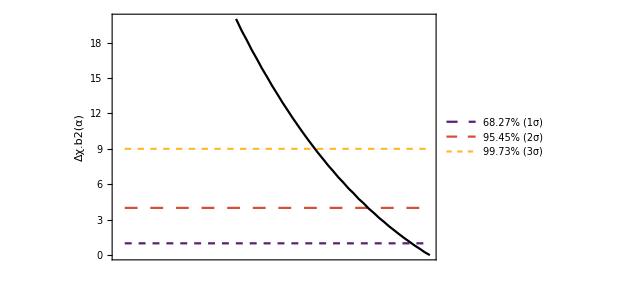

```mathematica
alphaplot=ListLinePlot[{{{alphapy[[1]][[1]],1.0},{alphapy[[-1]][[1]],1.0}},{{alphapy[[1]][[1]],4.0},{alphapy[[-1]][[1]],4.0}},{{alphapy[[1]][[1]],9.0},{alphapy[[-1]][[1]],9.0}},alphapy},LabelStyle->Directive[Black,Bold,10],Frame->True,FrameTicks->{{Automatic,Automatic},{None,Automatic}},PlotRange->{0,20},FrameLabel->{{"Δχ.b2(α)",""},{"",""}},PlotLegends-> Placed[LineLegend[{"68.27% (1σ)","95.45% (2σ)","99.73% (3σ)"},LegendMarkerSize->{30,10},LabelStyle->Directive[FontSize->12]],{0.8,0.7}],PlotStyle->{Directive[Dashed,RGBColor["#582078"]],Directive[Dashing[0.02],RGBColor["#d54e37"]],Directive[Dashing[0.01],RGBColor["#ffbb38"]],Black}]
```

```mathematica
Intervaloalpha=Graphics`Mesh`FindIntersections@alphaplot
```

{{0.887029,9.},{0.939256,4.},{0.982062,1.}}

```mathematica
AlphaSigma=Around[1,1-Intervaloalpha[[3]][[1]]]
```

1.0000.018

```mathematica
Alpha2Sigma=Around[1,1-Intervaloalpha[[2]][[1]]]
```

1.000.06

```mathematica
Alpha3Sigma=Around[1,1-Intervaloalpha[[1]][[1]]]
```

1.000.11

```mathematica
betapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/betapy_big.csv"] ;
```

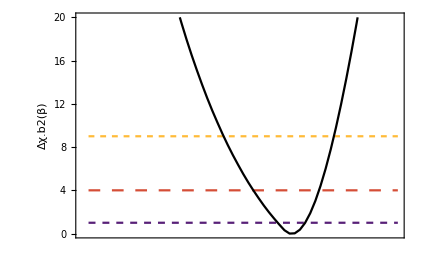

```mathematica
betaplot=ListLinePlot[{{{betapy[[1]][[1]],1.0},{betapy[[-1]][[1]],1.0}},{{betapy[[1]][[1]],4.0},{betapy[[-1]][[1]],4.0}},{{betapy[[1]][[1]],9.0},{betapy[[-1]][[1]],9.0}},betapy},LabelStyle->Directive[Black,Bold,10],Frame->True,FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{{Rotate["Δχ.b2(β)",180 Degree],""},{" ",""}},PlotLegends-> Placed[LineLegend[{"68.27% (1σ)","95.45% (2σ)","99.73% (3σ)"},LegendMarkerSize->{15,10},LabelStyle->Directive[FontSize->11]],{0.2,0.725},Rotate[#, 270 Degree]&],PlotStyle->{Directive[Dashed,RGBColor["#582078"]],Directive[Dashing[0.02],RGBColor["#d54e37"]],Directive[Dashing[0.01],RGBColor["#ffbb38"]],Black},PlotRange->{0,20}]
```

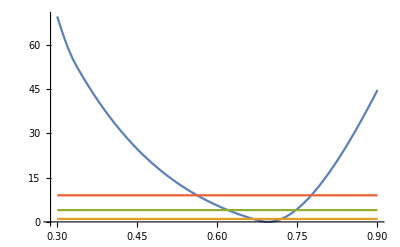

```mathematica
betaplot=ListLinePlot[{betapy,{{betapy[[1]][[1]],1.0},{betapy[[-1]][[1]],1.0}},{{betapy[[1]][[1]],4.0},{betapy[[-1]][[1]],4.0}},{{betapy[[1]][[1]],9.0},{betapy[[-1]][[1]],9.0}}}]
```

```mathematica
Intervalobeta=Graphics`Mesh`FindIntersections@betaplot
```

{{0.562036,9.},{0.619676,4.},{0.667029,1.},{0.720173,1.},{0.747024,4.},{0.775918,9.}}

```mathematica
BetaSigma=Around[0.69,{0.69-Intervalobeta[[3]][[1]], Intervalobeta[[4]][[1]]-0.69}]
```

0.6900.0230.030

```mathematica
BetaSigma2=Around[0.69,{0.69-Intervalobeta[[2]][[1]], Intervalobeta[[5]][[1]]-0.69}]
```

0.690.070.06

```mathematica
BetaSigma3=Around[0.69,{0.69-Intervalobeta[[1]][[1]], Intervalobeta[[6]][[1]]-0.69}]
```

0.690.130.09

```mathematica
Deltapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/Deltapy_big.csv"] ;
```

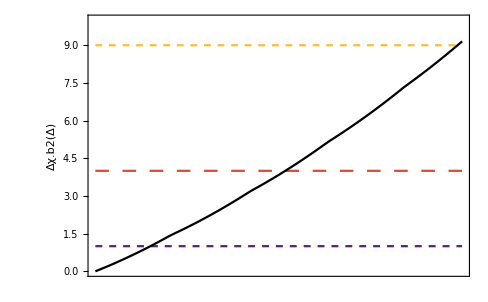

```mathematica
deltaplot=ListLinePlot[{{{Deltapy[[1]][[1]],1.0},{Deltapy[[-1]][[1]],1.0}},{{Deltapy[[1]][[1]],4.0},{Deltapy[[-1]][[1]],4.0}},{{Deltapy[[1]][[1]],9.0},{Deltapy[[-1]][[1]],9.0}},Deltapy},LabelStyle->Directive[Black,Bold,10],Frame->True,FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{{Rotate["Δχ.b2(Δ)",180 Degree],""},{" ",""}},PlotLegends-> Placed[LineLegend[{"68.27% (1σ)","95.45% (2σ)","99.73% (3σ)"},LegendMarkerSize->{15,10},LabelStyle->Directive[FontSize->11]],{0.2,0.65},Rotate[#, 270 Degree]&],PlotStyle->{Directive[Dashed,RGBColor["#582078"]],Directive[Dashing[0.02],RGBColor["#d54e37"]],Directive[Dashing[0.01],RGBColor["#ffbb38"]],Black},PlotRange->{0,10}]
```

```mathematica
Intervalodelta=Graphics`Mesh`FindIntersections@deltaplot
```

{{0.00449884,1.},{0.0155365,4.},{0.0296296,9.}}

```mathematica
DeltaSigma=Around[0.0,Intervalodelta[[1]][[1]]-0.0]
```

0.0000.004

```mathematica
Delta2Sigma=Around[0.0,Intervalodelta[[2]][[1]]-0.0]
```

0.0000.016

```mathematica
Delta3Sigma=Around[0.0,Intervalodelta[[3]][[1]]-0.0]
```

0.0000.030

```mathematica
alphabetapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/alpha_beta_py_big.csv"] ;
```

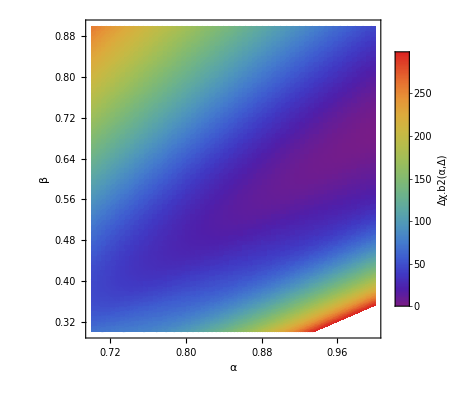

```mathematica
alphabetaplot=ListDensityPlot[alphabetapy,ColorFunction->"Rainbow",Mesh->70,MeshFunctions->{#3&},FrameLabel->{"α",Rotate["β",270 Degree]},LabelStyle->Directive[Black,Bold,10],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,Δ)",LegendMarkerSize->200],Right]]
```

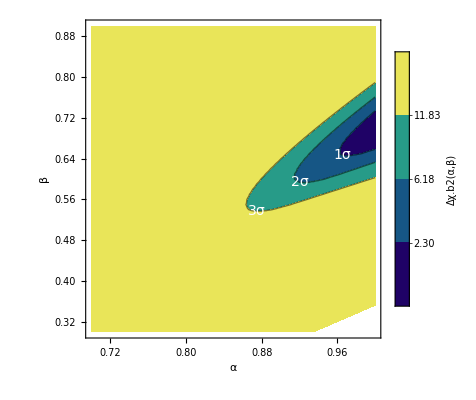

```mathematica
alphabetaCon=ListContourPlot[alphabetapy,Contours->{2.30,6.18,11.83},ContourLabels->(Text[Switch[#3,2.30,Style["1σ",FontColor->White,FontSize->14],6.18,Style["2σ",FontColor->White,FontSize->14],11.83,Style["3σ",FontColor->White,FontSize->14]],{#1,#2},Background->None]& ),ContourStyle->Directive[Black],FrameLabel->{"α",Rotate["β",270 Degree]},LabelStyle->Directive[Black,Bold,10],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,20}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,β)",LegendMarkerSize->200],Right]]
```

```mathematica
alphaDeltapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/alpha_Delta_py_big.csv"] ;
```

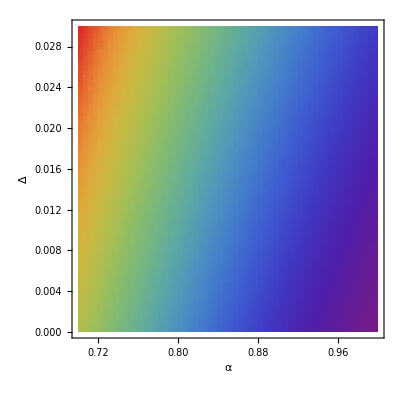

```mathematica
ListDensityPlot[alphaDeltapy,ColorFunction->"Rainbow",Mesh->25,MeshFunctions->{#3&},FrameLabel->{"α","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,Δ)"],Below],LabelStyle->Directive[Black,Bold,10]]
```

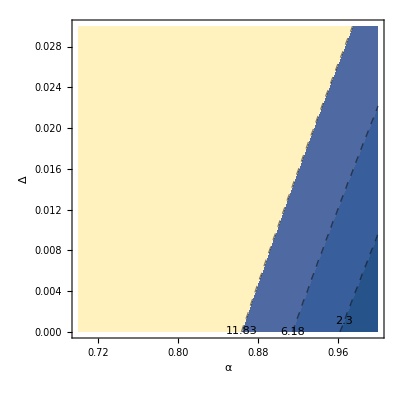

```mathematica
ListContourPlot[alphaDeltapy,Contours->{2.30,6.18,11.83},ContourLabels->True,ContourStyle->Directive[Dashed,Black],FrameLabel->{"α","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,Δ)"],Below],LabelStyle->Directive[Black,Bold,10]]
```

```mathematica
betaDeltapy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/beta_Delta_py_big.csv"] ;
```

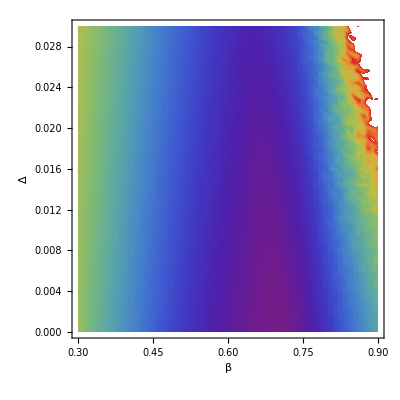

```mathematica
ListDensityPlot[betaDeltapy,ColorFunction->"Rainbow",Mesh->25,MeshFunctions->{#3&},FrameLabel->{"β","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(β,Δ)"],Below],LabelStyle->Directive[Black,Bold,10]]
```

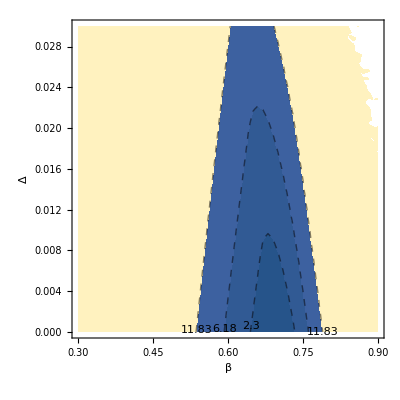

```mathematica
ListContourPlot[betaDeltapy,Contours->{2.30,6.18,11.83},ContourLabels->True,ContourStyle->Directive[Dashed,Black],FrameLabel->{"β","Δ"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(β,Δ)"],Below],LabelStyle->Directive[Black,Bold,10]]
```

```mathematica
{AlphaSigma,BetaSigma,DeltaSigma}
```

{1.0000.018,0.6900.0230.030,0.0000.004}

```mathematica
cm=72/2.54;
```

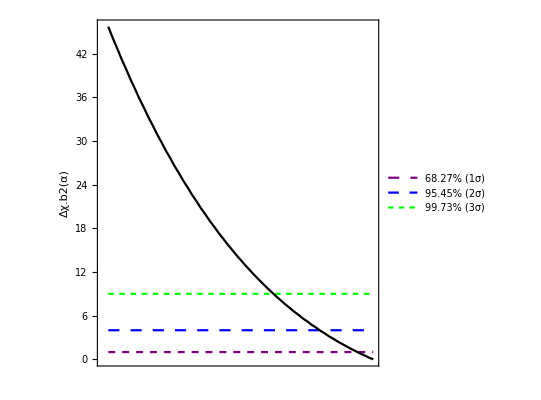
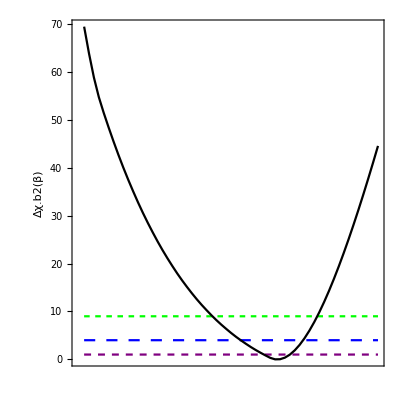
| -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Null,Show[alphaplot,AspectRatio->1,ImageSize->1-> {33cm, 0.12cm},ImagePadding->{{40, 70}, {10, 20}}]},{Rotate[Show[betaplot,AspectRatio->1,ImageSize->1-> {15cm, 0.12cm},ImagePadding->{{Automatic, -20}, {10, 0}}],90 Degree],Show[alphabetaplot,AspectRatio->1,ImageSize->1-> {33cm, 16cm}]}},Spacings->{-1.1,0}]
```

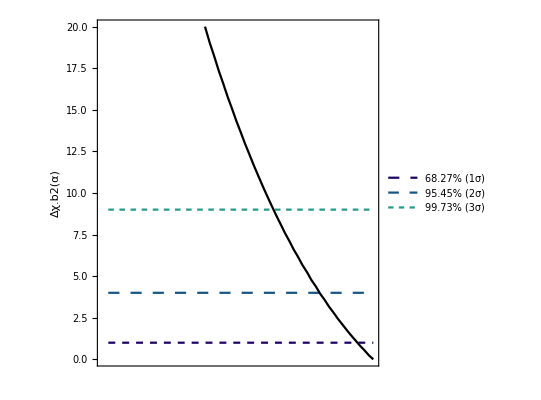
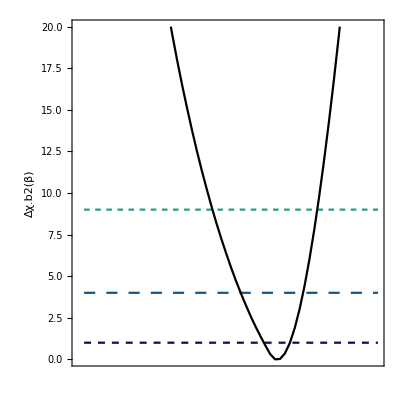
| -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Null,Show[alphaplot,AspectRatio->1,ImageSize->1-> {33cm, 0.275cm},ImagePadding->{{40, 75}, {10, 20}}]},{Rotate[Show[betaplot,AspectRatio->1,ImageSize->1-> {15cm, 0.32cm},ImagePadding->{{Automatic, -20}, {10, 0}}],90 Degree],Show[alphabetaCon,AspectRatio->1,ImageSize->1-> {33cm, 16cm}]}},Spacings->{-1.1,0}]
```

```mathematica
listContourDensityPlot[pList_,opts:OptionsPattern[]]:=Module[{pL,p,plotRangeRule,img,cont,densityOptions,contourOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[ListDensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,GridLines,Mesh,AspectRatio,PlotRangePadding,ImagePadding,Frame,Axes}]]],{PlotRangePadding->None,Frame->None,Axes->None,ImagePadding->None}];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Prolog,Epilog,FrameTicks,Background,ContourShading,Frame,Axes}]]],{Frame->None,Axes->None,ContourShading->False}];
(* //The density plot img and contour plot "cont" are created here:*)pL=ListDensityPlot[pList,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]]];
(* //Before showing the plots,set the PlotRange for the frame which will be drawn separately:*)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
(* //To align the image img with the contour plot,enclose img//in a bounding box rectangle of the same dimensions as cont,
//and then combine with cont using Show:*)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
alphabeta3=listContourDensityPlot[alphabetapy,Contours->{2.30,6.18,11.83},ContourLabels->(Text[Switch[#3,2.30,Style["1σ",FontColor->White,FontSize->14],6.18,Style["2σ",FontColor->White,FontSize->14],11.83,Style["3σ",FontColor->White,FontSize->14]],{#1,#2},Background->None]& ),ContourStyle->Directive[Black],FrameLabel->{"α",Rotate["β",270 Degree]},LabelStyle->Directive[Black,Bold,10],ColorFunctionScaling->False,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,20}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,β)",LegendMarkerSize->200],Right],Mesh->0,MeshFunctions->{#3&},AspectRatio->1,PlotRange->{Automatic,Automatic,{0,20}}]
```

-Graphics-

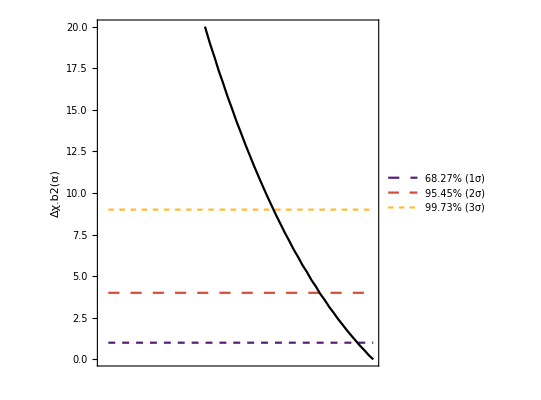
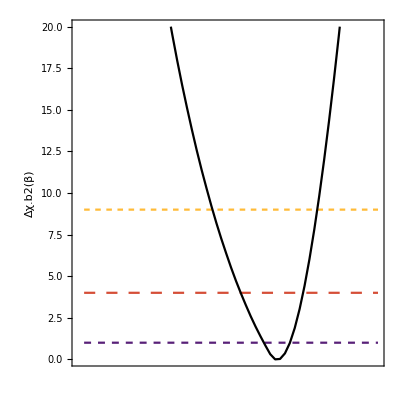
| -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Null,Show[alphaplot,AspectRatio->1,ImageSize->1-> {33cm, 0.275cm},ImagePadding->{{40, 75}, {10, 20}}]},{Rotate[Show[betaplot,AspectRatio->1,ImageSize->1-> {15cm, 0.32cm},ImagePadding->{{Automatic, -20}, {10, 8}}],90 Degree],Show[alphabeta3,AspectRatio->1,ImageSize->1-> {35.5cm, 16cm}]}},Spacings->{-0.6,0}]
```

```mathematica
alphadelta3=listContourDensityPlot[alphaDeltapy,Contours->{2.30,6.18,11.83},ContourLabels->(Text[Switch[#3,2.30,Style["1σ",FontColor->White,FontSize->14],6.18,Style["2σ",FontColor->White,FontSize->14],11.83,Style["3σ",FontColor->White,FontSize->14]],{#1,0.003},Background->None]& ),ContourStyle->Directive[Black],FrameLabel->{"α",Rotate["Δ",270 Degree]},LabelStyle->Directive[Black,Bold,10],ColorFunctionScaling->False,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,20}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(α,Δ)",LegendMarkerSize->200],Right],Mesh->0,MeshFunctions->{#3&},AspectRatio->1,PlotRange->{Automatic,Automatic,{0,20}}]
```

-Graphics-

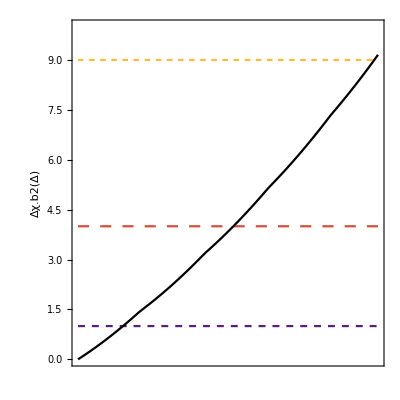
| -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Null,Show[alphaplot,AspectRatio->1,ImageSize->1-> {33cm, 0.275cm},ImagePadding->{{40, 65}, {10, 20}}]},{Rotate[Show[deltaplot,AspectRatio->1,ImageSize->1-> {340cm, 0.72cm},ImagePadding->{{Automatic, 0}, {10, 8}}],90 Degree],Show[alphadelta3,AspectRatio->1,ImageSize->1-> {35.5cm, 350cm}]}},Spacings->{-0.4,0}]
```

```mathematica
betadelta3=listContourDensityPlot[betaDeltapy,Contours->{2.30,6.18,11.83},ContourLabels->(Text[Switch[#3,2.30,Style["1σ",FontColor->White,FontSize->14],6.18,Style["2σ",FontColor->White,FontSize->14],11.83,Style["3σ",FontColor->White,FontSize->14]],{#1,0.005},Background->None]& ),ContourStyle->Directive[Black],FrameLabel->{"β",Rotate["Δ",270 Degree]},LabelStyle->Directive[Black,Bold,10],ColorFunctionScaling->False,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,20}]]&),PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δχ.b2(β,Δ)",LegendMarkerSize->200],Right],Mesh->0,MeshFunctions->{#3&},AspectRatio->1,PlotRange->{Automatic,Automatic,{0,20}}]
```

-Graphics-

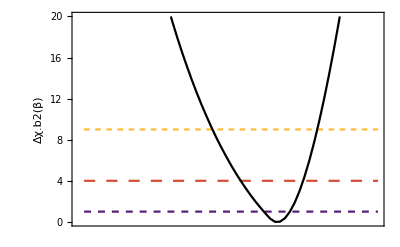

```mathematica
betaplot3=ListLinePlot[{{{betapy[[1]][[1]],1.0},{betapy[[-1]][[1]],1.0}},{{betapy[[1]][[1]],4.0},{betapy[[-1]][[1]],4.0}},{{betapy[[1]][[1]],9.0},{betapy[[-1]][[1]],9.0}},betapy},LabelStyle->Directive[Black,Bold,10],Frame->True,FrameTicks->{{Automatic,Automatic},{None,Automatic}},FrameLabel->{{Rotate["Δχ.b2(β)",0 Degree],""},{" ",""}},PlotLegends-> Placed[LineLegend[{"68.27% (1σ)","95.45% (2σ)","99.73% (3σ)"},LegendMarkerSize->{15,10},LabelStyle->Directive[FontSize->11]],{0.2,0.725},Rotate[#, 0]&],PlotStyle->{Directive[Dashed,RGBColor["#582078"]],Directive[Dashing[0.02],RGBColor["#d54e37"]],Directive[Dashing[0.01],RGBColor["#ffbb38"]],Black},PlotRange->{0,20}]
```

```mathematica
Grid[{{Null,Show[betaplot3,AspectRatio->1,ImageSize->1-> {18cm, 0.275cm},ImagePadding->{{40, 65}, {10, 20}}]},{Rotate[Show[deltaplot,AspectRatio->1,ImageSize->1-> {340cm, 0.72cm},ImagePadding->{{Automatic, 0}, {10, 8}}],90 Degree],Show[betadelta3,AspectRatio->1,ImageSize->1-> {19cm, 350cm}]}},Spacings->{-0.4,0}]
```

| -Graphics-
-Graphics- | -Graphics-